## Special cases for the γ parameters

The case where γ_2=γ_1 is not good, from the restriction leads to G(r) = A(r), so it is not possible to find a solution
The case where γ_2=2γ_1 is good.

```mathematica
eq1:=X[r]+2G[r]-2A[r]==Subscript[γ, 1];
eq2:=X'[r]-2A'[r]-2G[r]A[r]+2G[r]X[r]-2 G[r]^2==X'[r]-2G'[r]+G[r]X[r]-G[r]A[r]-2 G[r]^2-A[r]^2+A[r]X[r];
eq3:=A[r]+X[r]-G[r]==2 Subscript[γ, 1];
FullSimplify[eq1]
FullSimplify[eq2]
FullSimplify[eq3]
```

2 A[r]+γ_1==2 G[r]+X[r]

(A[r]-G[r]) (A[r]-X[r])+2 G'[r]==2 A'[r]

A[r]+X[r]==G[r]+2 γ_1

```mathematica
Solve[eq1,X[r]]
```

{{X[r]→2 A[r]-2 G[r]+γ_1}}

```mathematica
X[r_]:=2A[r]-2 G[r]+Subscript[γ, 1];
FullSimplify[eq1]
FullSimplify[eq2]
FullSimplify[eq3]
```

True

(A[r]-G[r]) (A[r]-2 G[r]+γ_1)+2 (A'[r]-G'[r])==0

3 A[r]==3 G[r]+γ_1

```mathematica
Solve[eq3,A[r]]
```

{{A[r]→1/3 (3 G[r]+γ_1)}}

```mathematica
A[r_]:=1/3 (3 G[r]+Subscript[γ, 1]);
FullSimplify[eq1]
FullSimplify[eq2]
FullSimplify[eq3]
```

True

3 G[r] γ_1==4 γ_1^2

True

```mathematica
FullSimplify[DSolve[eq2,G[r],r]]
```

{{G[r]→(4 γ_1)/3}}

```mathematica
G[r_]:=(4 Subscript[γ, 1])/3;
FullSimplify[eq1]
FullSimplify[eq2]
FullSimplify[eq3]
```

True

True

True

```mathematica
FullSimplify[A[r]]
FullSimplify[G[r]]
FullSimplify[X[r]]
```

(5 γ_1)/3

(4 γ_1)/3

(5 γ_1)/3

```mathematica
HC1:=B''[r]+B'[r]*(X[r]+2*G[r]-2*A[r])+2*B[r]*(G[r]*(X[r]-A[r]-G[r])-A'[r]+X'[r]/2);
HC2:=F''[r]+F'[r]*(A[r]+X[r]-G[r])+F[r]*(X'[r]-2*G[r]^2+(A[r]+G[r])*(X[r]-A[r]))-G[r];
FullSimplify[HC1==0]
FullSimplify[DSolve[HC1==0,B[r],r]]
FullSimplify[HC2==0]
FullSimplify[DSolve[HC2==0,F[r],r]]
```

32 B[r] γ_1^2==9 (γ_1 B'[r]+B''[r])

{{B[r]→ⅇ^(-1/6 (3+√137) r γ_1) (C[1]+ⅇ^(1/3 √137 r γ_1) C[2])}}

2 γ_1 (6+16 F[r] γ_1-9 F'[r])==9 F''[r]

{{F[r]→ⅇ^(-1/3 (3+√41) r γ_1) (C[1]+ⅇ^(2/3 √41 r γ_1) C[2])-3/(8 γ_1)}}

```mathematica
B[r_]:=ⅇ^(-1/6 (3+√137) r Subscript[γ, 1]) (C[1]+ⅇ^(1/3 √137 r Subscript[γ, 1]) C[2]);
F[r_]:=ⅇ^(-1/3 (3+√41) r Subscript[γ, 1]) (C[1]+ⅇ^(2/3 √41 r Subscript[γ, 1]) C[2])-3/(8 Subscript[γ, 1]);
```

```mathematica
Rtt[r_]:=B'[r]+B[r]*(2*G[r]+X[r]-A[r]);
Rrr[r_]:=A'[r]+2G'[r]+A[r]A[r]+2G[r]G[r]-A[r]X[r]-2X[r]G[r];
Rthth[r_]:=F'[r]+F[r](A[r]+X[r])+1;
FullSimplify[Rtt[r]]
FullSimplify[Rrr[r]]
FullSimplify[Rthth[r]]
```

1/6 ⅇ^(-1/6 (3+√137) r γ_1) (-(-13+√137) C[1]+(13+√137) ⅇ^(1/3 √137 r γ_1) C[2]) γ_1

-(8 γ_1^2)/9

-1/4+1/3 ⅇ^(-1/3 (3+√41) r γ_1) (-(-7+√41) C[1]+(7+√41) ⅇ^(2/3 √41 r γ_1) C[2]) γ_1

## Auto-parallel curves

```mathematica
eq1t[τ_]:=t''[τ]+2*A[r[τ]]*r'[τ]*t'[τ];
FullSimplify[eq1t[τ]]
eq1r[τ_]=r''[τ]+B[r[τ]]*t'[τ]^2+X[r[τ]]*r'[τ]^2+F[r[τ]]*θ'[τ]^2+F[r[τ]]*ϕ'[τ]^2*Sin[θ]^2;
FullSimplify[eq1r[τ]]
eq1th[τ_]=θ''[τ]+2*G[r[τ]]*θ'[τ]*r'[τ]-Cos[θ]*Sin[θ]*ϕ'[τ]^2;
FullSimplify[eq1th[τ]]
eq1ph[τ_]=ϕ''[τ]+2*G[r[τ]]*ϕ'[τ]*r'[τ]+Cos[θ]/Sin[θ]*ϕ'[τ]*θ'[τ];
FullSimplify[eq1ph[τ]]
```

10/3 γ_1 r'[τ] t'[τ]+t''[τ]

5/3 γ_1 r'[τ]^2+ⅇ^(-1/6 (3+√137) r[τ] γ_1) (C[1]+ⅇ^(1/3 √137 r[τ] γ_1) C[2]) t'[τ]^2+ⅇ^(-1/3 (3+√41) r[τ] γ_1) (C[1]+ⅇ^(2/3 √41 r[τ] γ_1) C[2]) (θ'[τ]^2+Sin[θ]^2 ϕ'[τ]^2)-(3 (θ'[τ]^2+Sin[θ]^2 ϕ'[τ]^2))/(8 γ_1)+r''[τ]

8/3 γ_1 r'[τ] θ'[τ]-Cos[θ] Sin[θ] ϕ'[τ]^2+θ''[τ]

8/3 γ_1 r'[τ] ϕ'[τ]+Cot[θ] θ'[τ] ϕ'[τ]+ϕ''[τ]

Fixing θ=π/2

```mathematica
eq1t[τ_]:=t''[τ]+2*A[r[τ]]*r'[τ]*t'[τ];
FullSimplify[eq1t[τ]]
eq1r[τ_]=r''[τ]+B[r[τ]]*t'[τ]^2+X[r[τ]]*r'[τ]^2+F[r[τ]]*ϕ'[τ]^2;
FullSimplify[eq1r[τ]]
eq1ph[τ_]=ϕ''[τ]+2*G[r[τ]]*ϕ'[τ]*r'[τ];
FullSimplify[eq1ph[τ]]
```

10/3 γ_1 r'[τ] t'[τ]+t''[τ]

5/3 γ_1 r'[τ]^2+ⅇ^(-1/6 (3+√137) r[τ] γ_1) (C[1]+ⅇ^(1/3 √137 r[τ] γ_1) C[2]) t'[τ]^2+(ⅇ^(-1/3 (3+√41) r[τ] γ_1) (C[1]+ⅇ^(2/3 √41 r[τ] γ_1) C[2])-3/(8 γ_1)) ϕ'[τ]^2+r''[τ]

8/3 γ_1 r'[τ] ϕ'[τ]+ϕ''[τ]

```mathematica
DSolve[8/3 Subscript[γ, 1] r'[τ] ϕ'[τ]+ϕ''[τ]==0,ϕ[τ],τ]
```

{{ϕ[τ]→C[2]+ⅇ^(-8/3 r[K[1]] γ_1) C[1]K[1]1τ}}

```mathematica
D[C[2]+ⅇ^(-8/3 r[K[1]] Subscript[γ, 1]) C[1]K[1]1τ,τ]
```

ⅇ^(-8/3 r[τ] γ_1) C[1]

```mathematica
ϕ[τ_]:=C[2]+ⅇ^(-8/3 r[K[1]] Subscript[γ, 1]) C[1]K[1]1τ;
eq1t[τ_]:=t''[τ]+2*A[r[τ]]*r'[τ]*t'[τ];
FullSimplify[eq1t[τ]]
eq1r[τ_]=r''[τ]+B[r[τ]]*t'[τ]^2+X[r[τ]]*r'[τ]^2+F[r[τ]]*ϕ'[τ]^2;
FullSimplify[eq1r[τ]]
eq1ph[τ_]=ϕ''[τ]+2*G[r[τ]]*ϕ'[τ]*r'[τ];
FullSimplify[eq1ph[τ]]
```

10/3 γ_1 r'[τ] t'[τ]+t''[τ]

ⅇ^(-16/3 r[τ] γ_1) C[1]^2 (ⅇ^(-1/3 (3+√41) r[τ] γ_1) (C[1]+ⅇ^(2/3 √41 r[τ] γ_1) C[2])-3/(8 γ_1))+5/3 γ_1 r'[τ]^2+ⅇ^(-1/6 (3+√137) r[τ] γ_1) (C[1]+ⅇ^(1/3 √137 r[τ] γ_1) C[2]) t'[τ]^2+r''[τ]

0

```mathematica
DSolve[10/3 Subscript[γ, 1] r'[τ] t'[τ]+t''[τ]==0,t[τ],τ]
```

{{t[τ]→C[2]+ⅇ^(-10/3 r[K[1]] γ_1) C[1]K[1]1τ}}

```mathematica
D[C[2]+ⅇ^(-10/3 r[K[1]] Subscript[γ, 1]) C[1]K[1]1τ,τ]
```

ⅇ^(-10/3 r[τ] γ_1) C[1]

```mathematica
t[τ_]:=C[2]+ⅇ^(-10/3 r[K[1]] Subscript[γ, 1]) C[1]K[1]1τ;
eq1t[τ_]:=t''[τ]+2*A[r[τ]]*r'[τ]*t'[τ];
FullSimplify[eq1t[τ]]
eq1r[τ_]=r''[τ]+B[r[τ]]*t'[τ]^2+X[r[τ]]*r'[τ]^2+F[r[τ]]*ϕ'[τ]^2;
FullSimplify[eq1r[τ]]
eq1ph[τ_]=ϕ''[τ]+2*G[r[τ]]*ϕ'[τ]*r'[τ];
FullSimplify[eq1ph[τ]]
```

0

ⅇ^(-1/6 (43+√137) r[τ] γ_1) C[1]^2 (C[1]+ⅇ^(1/3 √137 r[τ] γ_1) C[2])+ⅇ^(-16/3 r[τ] γ_1) C[1]^2 (ⅇ^(-1/3 (3+√41) r[τ] γ_1) (C[1]+ⅇ^(2/3 √41 r[τ] γ_1) C[2])-3/(8 γ_1))+5/3 γ_1 r'[τ]^2+r''[τ]

0

A numerical solution to the above differential equation

-1/8 ⅇ^(-(19 r[τ])/3) (3 ⅇ^r[τ]+16 Cosh[1/3 √41 r[τ]])-2 ⅇ^(-(43 r[τ])/6) Cosh[1/6 √137 r[τ]]+5/3 r'[τ]^2+r''[τ]

{{r[τ]→InterpolatingFunction[…][τ]}}

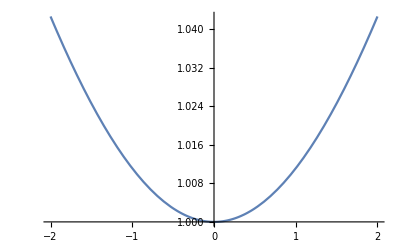

```mathematica
Subscript[γ, 1]=1;
eq1r[τ_]=r''[τ]+B[r[τ]]*t'[τ]^2+X[r[τ]]*r'[τ]^2+F[r[τ]]*ϕ'[τ]^2;
FullSimplify[eq1r[τ]/.{C[1]->-1,C[2]->-1,C[3]->-100}]
s=NDSolve[{%==0,r[0]==1,r'[0]==0},r[τ],{τ,-2,2}]
Plot[r[τ]/.s,{τ,-2,2}]
```

1/8 ⅇ^(-(19 r[τ])/3) (-3 ⅇ^r[τ]+16 Cosh[1/3 √41 r[τ]])+2 ⅇ^(-(43 r[τ])/6) Cosh[1/6 √137 r[τ]]+5/3 r'[τ]^2+r''[τ]

{{r[τ]→InterpolatingFunction[…][τ]}}

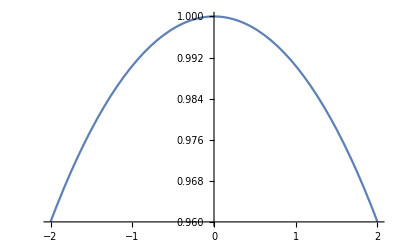

```mathematica
eq1r[τ_]=r''[τ]+B[r[τ]]*t'[τ]^2+X[r[τ]]*r'[τ]^2+F[r[τ]]*ϕ'[τ]^2;
FullSimplify[eq1r[τ]/.{C[1]->1,C[2]->1,C[3]->1}]
s=NDSolve[{%==0,r[0]==1,r'[0]==0},r[τ],{τ,-2,2}]
Plot[r[τ]/.s,{τ,-2,2}]
```

```mathematica
FullSimplify[Rtt[r]]
FullSimplify[Rrr[r]]
FullSimplify[Rthth[r]]
```

1/6 ⅇ^(-1/6 (3+√137) r) (-(-13+√137) C[1]+(13+√137) ⅇ^((√137 r)/3) C[2])

-8/9

1/12 ⅇ^(-1/3 (3+√41) r) (-3 ⅇ^(1/3 (3+√41) r)-4 (-7+√41) C[1]+4 (7+√41) ⅇ^((2 √41 r)/3) C[2])

In the limit for r to infinity

```mathematica
Limit[Rtt[r],r->∞]
FullSimplify[Limit[Rrr[r],r->∞]]
Limit[Rthth[r],r->∞]
```

C[2] ∞

-8/9

C[2] ∞

De Sitter metric

```mathematica
gtt[r_]:=-(1-(2*a)/r-b*r^2);
grr[r_]:=1/(1-(2*a)/r-b*r^2) ;
gthth[r_]:=r^2;
Limit[gtt[r],r->∞]
FullSimplify[Limit[grr[r],r->∞]]
Limit[gthth[r],r->∞]
```

b ∞

0

∞

Anti de Sitter

```mathematica
gtt[r_]:=-(1-a/r+b*r^2);
grr[r_]:=1/(1-a/r+b*r^2) ;
gthth[r_]:=r^2;
gthth[r_]:=r^2;
Limit[gtt[r],r->∞]
FullSimplify[Limit[grr[r],r->∞]]
Limit[gthth[r],r->∞]
```

b (-∞)

0

∞